# Projectiles and Charged Particles

## Juan Jose Neri

### Problem 2.43

-Graphics-

-Graphics-

-Graphics-

Let us first solve for the constants

```mathematica
g=9.8;
γ=0.25;
c[d_]:=γ d^2;
c[0.24]
```

0.0144

Here in this problem m=0,6Kg  and therefore the above equations become

```mathematica
v0=15;
vx0=N[v0*Cos[Pi/4]];
vy0=N[v0*Sin[Pi/4]];
```

```mathematica
Sol=NDSolve[
{0.6*vx'[t]+0.0144*√(vx[t]^2+vy[t]^2)vx[t]==0,
0.6*vy'[t]+0.6+0.0144*√(vx[t]^2+vy[t]^2)vy[t]==0,
vx[0]==vx0,vy[0]==vy0},
{vx,vy},{t,0,25}
]
```

{{vx→InterpolatingFunction[{{0., 25.}}, <>],vy→InterpolatingFunction[{{0., 25.}}, <>]}}

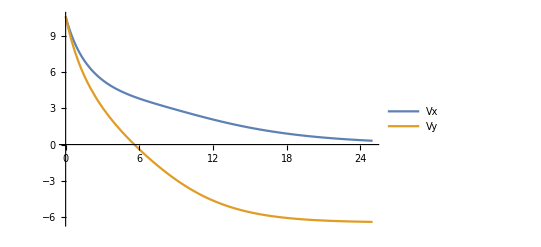

```mathematica
Plot[Evaluate[{vx[t],vy[t]}/.Sol],{t,0,25},PlotRange->All,PlotLegends->{"Vx","Vy"}]
```